MathematicaIO warning: redefining field speed.
Field origin defaults to {0,0}
Field sndOrder defaults to 0
Fast marching solver completed in 0.000248 s.
Field exportActiveNeighs defaults to 0
Field exportGeodesicFlow defaults to 0
Unused fields : MaxStencilWidth StencilCPUTime nAccepted 
Defaulted fields : Hi activeNeighs euclideanScale exportActiveNeighs exportGeodesicFlow getStencils indexToPoint inspectSensitivity nMaxAccepted origin pointToIndex progressReportLandmarks seedFlags seedValueVariation seedValues seeds_Unoriented sndOrder speedVariation stopAtDistance stopWhenAllAccepted stopWhenAnyAccepted tips tips_Unoriented values walls

{False,True}

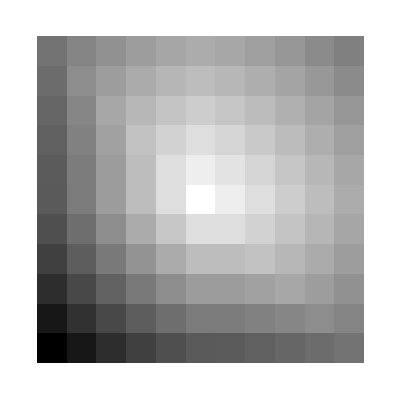

```mathematica
Module[{params=Association[{}],n=11,values,test,used,defaulted},
params["model"]="IsotropicBox2<Boundary::Closed>";
params["speed"]=Array[1.&,{n,n}];
params["dims"]={n,n};
params["gridScale"]=1./n;
params["seeds"]={{0.5,0.5}};
params["exportValues"]=1.;

LoadHFMWLL[hfmLibraryPath];
hfmSetVariable[#1,#2]&@@@Normal[params];
hfmSetVariable["speed",Array[If[#1>#2,1.,2.]&,{n,n}]];
hfmSetVariable["verbosity",2];
hfmRunModel[];
values=hfmGetArray[2]["values"];
Print[hfmHasField/@{"Hi","MaxStencilWidth"}];
hfmEraseField["FMCPUTime"];
UnloadHFMWLL[];
ArrayPlot[values]
]
```

```mathematica
Print["Hi"];Print["There"];
```

Hi

There

```mathematica
Head[True]
```

Symbol